Properties of finite amplitude electromagnetic waves propagating in the quantum vacuum

Hedvika Kadlecová, Sergei V Bulanov and Georg Korn, Plasma Phys. Control. Fusion 61 084002 (2019)
https://doi.org/10.1088/1361-6587/ab21fb
Notebook: Óscar Amaro, June 2021, November 2022 @ GoLP-EPP
Contact: oscar.amaro@tecnico.ulisboa.pt

Introduction
In this notebook we reproduce some results from the paper.

## Prove eq 16+17 is equivalent to eq 13+14 ...

```mathematica
(* eq 16 is the easiest to prove *)
Clear[Ε,Β,E0,B0,Ez,By,a,b,x,t,α,β,γ]

(* eq 15 *)
Ez[x,t]=E0+a[x,t];
By[x,t]=B0+b[x,t];

(* eq 13 *)
D[By[x,t],t]-D[Ez[x,t],x]
```

b^(0,1)[x,t]-a^(1,0)[x,t]

```mathematica
(* eq 17 requires a bit more work ... *)
Clear[Ε,Β,E0,B0,Ez,By,a,b,x,t,α,β,γ,eq14,eq17,κ1,κ2]
κ2=180/315 κ1;

(* eq 15 *)
Ez[x,t]=E0+a[x,t];
By[x,t]=B0+b[x,t];

(* eq 14 *)
eq14=-(1+8κ1 Ez[x,t]^2+4(Ez[x,t]^2-By[x,t]^2)(κ1-3κ2 Ez[x,t]^2)-6κ2(Ez[x,t]^2-By[x,t]^2)^2)D[Ez[x,t],t]+(1-8κ1 By[x,t]^2+4(Ez[x,t]^2-By[x,t]^2)(κ1+3κ2 By[x,t]^2)-6κ2(Ez[x,t]^2-By[x,t]^2)^2)D[By[x,t],x]+4(2κ1-3κ2(Ez[x,t]^2-By[x,t]^2))Ez[x,t] By[x,t](D[By[x,t],t]+D[Ez[x,t],x])//Expand//Simplify;

(* eq 18 *)
α=1+8κ1(E0+a[x,t])^2+4((E0+a[x,t])^2-(B0+b[x,t])^2)(κ1-3(E0+a[x,t])^2 κ2)-6κ2((E0+a[x,t])^2-(B0+b[x,t])^2)^2;
(* eq 19 *)
β=4(E0+a[x,t])(B0+b[x,t])(2κ1-3κ2((E0+a[x,t])^2-(B0+b[x,t])^2));
(* eq 20 *)
γ=1-8κ1(B0+b[x,t])^2+4((E0+a[x,t])^2-(B0+b[x,t])^2)(κ1+3(B0+b[x,t])^2 κ2)-6κ2((E0+a[x,t])^2-(B0+b[x,t])^2);

(* eq 17 *)
eq17=α D[a[x,t],t]-β(D[a[x,t],x]+D[b[x,t],t])-γ D[b[x,t],x]//Expand//Simplify;

(* confirm eq 21 *)
{α,β,γ}/.{a[x,t]->0,b[x,t]->0,B0->E0}

res=eq14/eq17;
(res/.{Derivative[0,1][b][x,t]->Derivative[1,0][a][x,t]})//FullSimplify

(*
E0=RandomReal[];
B0=RandomReal[];
κ1=RandomReal[];
res//FullSimplify
*)
```

{1+8 E0^2 κ1,8 E0^2 κ1,1-8 E0^2 κ1}

((7-4 (7+6 B0^2-6 E0^2) (B0^2-3 E0^2) κ1+4 κ1 (-72 E0 a[x,t]^3-18 a[x,t]^4-b[x,t] (2 B0+b[x,t]) (7+12 B0^2-24 E0^2+6 b[x,t] (2 B0+b[x,t]))+3 a[x,t]^2 (7+8 B0^2-36 E0^2+8 b[x,t] (2 B0+b[x,t]))+6 E0 a[x,t] (7+8 B0^2-12 E0^2+8 b[x,t] (2 B0+b[x,t])))) a^(0,1)[x,t]-7 b^(1,0)[x,t]+4 κ1 (7+6 B0^2-6 E0^2-6 a[x,t] (2 E0+a[x,t])+6 b[x,t] (2 B0+b[x,t])) (-4 (E0+a[x,t]) (B0+b[x,t]) a^(1,0)[x,t]-(-3 B0^2+E0^2+2 E0 a[x,t]+a[x,t]^2-3 b[x,t] (2 B0+b[x,t])) b^(1,0)[x,t]))/((-7+4 (7+6 B0^2-6 E0^2) (B0^2-3 E0^2) κ1+4 κ1 (72 E0 a[x,t]^3+18 a[x,t]^4+b[x,t] (2 B0+b[x,t]) (7+12 B0^2-24 E0^2+6 b[x,t] (2 B0+b[x,t]))-3 a[x,t]^2 (7+8 B0^2-36 E0^2+8 b[x,t] (2 B0+b[x,t]))-6 E0 a[x,t] (7+8 B0^2-12 E0^2+8 b[x,t] (2 B0+b[x,t])))) a^(0,1)[x,t]+16 κ1 (E0+a[x,t]) (B0+b[x,t]) (7+6 B0^2-6 E0^2-6 a[x,t] (2 E0+a[x,t])+6 b[x,t] (2 B0+b[x,t])) a^(1,0)[x,t]+(7+4 (E0^2-3 B0^2 (5+4 B0^2-4 E0^2)) κ1+4 κ1 (-3 b[x,t] (2 B0+b[x,t]) (5+8 B0^2-4 E0^2+4 b[x,t] (2 B0+b[x,t]))+2 E0 a[x,t] (1+12 B0^2+12 b[x,t] (2 B0+b[x,t]))+a[x,t]^2 (1+12 B0^2+12 b[x,t] (2 B0+b[x,t])))) b^(1,0)[x,t])

```mathematica
(* get eq 23 *)
Clear[eq16,eq17,x,t,a,b,α,β,γ,aa,bb,ν,q,ω,α0,β0,γ0]
(* eq 22 ansatz *)
a[x,t]=aa Exp[-I ω t+I q x];
b[x,t]=bb Exp[-I ω t+I q x];

eq16=D[b[x,t],t]-D[a[x,t],x]//Simplify;
eq17=α D[a[x,t],t]-β(D[a[x,t],x]+D[b[x,t],t])-γ D[b[x,t],x]//Expand//Simplify;
ω=ν q;
(* *)
eq16/(aa+ν bb)//Simplify
eq17/(ν(bb β-aa α)-(aa β+bb γ))//FullSimplify
```

-ⅈ ⅇ^(ⅈ q (x-t ν)) q

ⅈ ⅇ^(ⅈ q (x-t ν)) q

```mathematica
(* Taylor expand eq 69 ... *)
Clear[κ1,E0,E02]
Series[(1-8κ1 E0^2)/(1+8 κ1 E0^2),{ E0,0,4}]
(1-8κ1 E02)(1-8 κ1 E02)//Expand
```

1-16 κ1 E0^2+128 κ1^2 E0^4+O[E0]^5

1-16 E02 κ1+64 E02^2 κ1^2

```mathematica
(* get eq 24 *)
Clear[a,b,ν,α0,β0,γ0,sol]
a=-ν b;
sol=Solve[ν(b β0-a α0)-(a β0+b γ0)==0,ν]

(* use relationships by equation 21 *)
{α0,β0,γ0}={1+8 E0^2 κ1,8 E0^2 κ1,1-8 E0^2 κ1};
(* get eq 25 *)
sol//Simplify
```

{{ν→(-β0-√(β0^2+α0 γ0))/α0},{ν→(-β0+√(β0^2+α0 γ0))/α0}}

{{ν→-1},{ν→(1-8 E0^2 κ1)/(1+8 E0^2 κ1)}}

```mathematica
(* get eq 71 ... *)
(*
Clear[κ1,κ2,E0,ν,fp]
ν=(1-8κ1 E0^2)/(1+8 κ1 E0^2);
fp=4E0(κ1(-1-3ν-3 ν^2+3/ν)+3κ2 E0^2(ν^2+3ν-3+1/ν))//Simplify;
*)

Clear[κ1,κ2,E0,ν,fp]
(* the correct coefficient of E0^4 will not change eq 71 *)
ν=1-16κ1 E0^2+128 κ1^2 E0^4;
fp=4E0(κ1(-1-3ν-3 ν^2+3/ν)+3κ2 E0^2(ν^2+3ν-3+1/ν))//Expand;

(* f' will not be a polynome in E0 because of the rational form of ν *)

(* this is not equal to eq 71 ...*)
CoefficientList[Normal[Series[fp,{E0,0,4}]]-48 E0^3(12 κ1^2+κ2)//Expand,E0][[4]]

(* but 48 E0^3(16 κ1^2+0.5κ2) is *)
Normal[Series[fp,{E0,0,4}]]-48 E0^3(16 κ1^2+0.5κ2)//Expand
```

192 κ1^2-24 κ2

0.-16 E0 κ1

## Figure 1: visualize eq 73

x0+t (1+am fp Sin[x0])

t

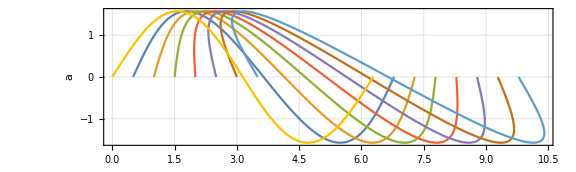

```mathematica
Clear[a0,am,fp,x,t]

a0=am Sin[x0];
x=x0+(1+fp a0)t

(* a(x,x0=0) is the first (to the left) point of each curve. for Δt=0.5 (difference in time is uniform for all curves) then a(x,x0=0) progresses linearly. the first blue curve for lowest time is for t=0.5 and not t=0 *)
x/.{x0->0}

(* looking at the plot, the amplitude am cannot be 1, but needs to be around 1.5, which is very close to π/2 *)
am=π/2; 
fp=-0.35;

tab=Table[{x,a0//N},{x0,0,2π,2π/100}];
ListPlot[{(tab/.{t->0.5}),(tab/.{t->1}),(tab/.{t->1.5}),(tab/.{t->2}),(tab/.{t->2.5}),(tab/.{t->3}),(tab/.{t->3.5}),(tab/.{t->0})},Joined->True,Frame->True,FrameLabel->{"x","a"},GridLines->Automatic,AspectRatio->0.3,ImageSize->Large]
```

## Figure 3

```mathematica
(* eq 87 *)
Clear[a1,a10,t,fp]
DSolve[{D[a1[t],t]==-fp a1[t]^2,a1[0]==a10},a1[t],t]
```

{{a1[t]→a10/(1+a10 fp t)}}

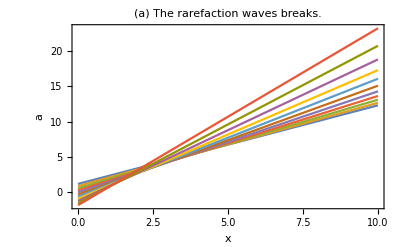

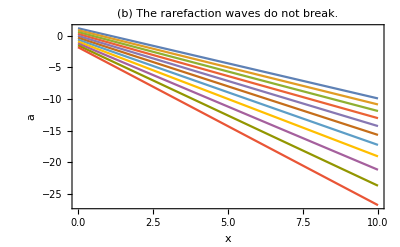

```mathematica
Clear[a0,a1,a10,fp,tab]
a1[t_,a10_,fp_]:=a10/(1+fp a10 t)
a[x_,t_,a0_,a10_,fp_]:=a0+a1[t,a10,fp]x

(* a) *)
tab=Table[a[x,t,-3t+1.8,1,-0.5],{t,0.2,1.2,0.1}];
Plot[tab,{x,0,10},Frame->True,FrameLabel->{"x","a"},PlotLabel->"(a) The rarefaction waves breaks."]

(* b) *)
tab=Table[a[x,t,-3t+1.8,-1,0.5],{t,0.2,1.2,0.1}];
Plot[tab,{x,0,10},Frame->True,FrameLabel->{"x","a"},PlotLabel->"(b) The rarefaction waves do not break."]
```

## Figure 4

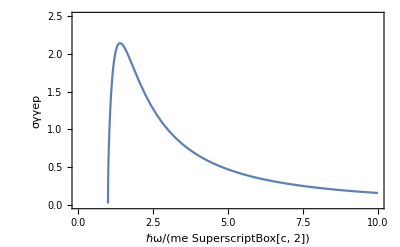

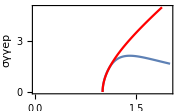

```mathematica
(* σγγep in "natural" units, and assuming ω=Ω or ω1=ω2 *)
Clear[σγγep,re,e,me,c,ℏ,ω,βe]
βe=Sqrt[1-(me^2 c^4)/(ℏ^2 ω^2)];
σγγep=(π re^2)/2(1-βe^2)((3-βe^4)Log[(1+βe)/(1-βe)]-2βe(2-βe^2));
re=e^2/(me c^2);
e=me=c=ℏ=1;
Plot[σγγep,{ω,0,10},PlotRange->{0,2.5},Frame->True,FrameLabel->{"ℏω/(me SuperscriptBox[c, 2])","σγγep"}]

Plot[{σγγep,π re^2 Sqrt[(ℏ^2 ω^2)/(me^2 c^4)-1]},{ω,0,2},PlotRange->{{0,2},{0,5}},Frame->True,FrameLabel->{"ℏω/(me SuperscriptBox[c, 2])","σγγep"},ImageSize->Small,PlotLegends->{"Exact cross section: eq 90","Near-threshold: eq 89"},PlotStyle->{Automatic,Red}]
```